## Usage

## Initialize

```mathematica
$HistoryLength=1;
ClearAll["Global`*"];
Off[General::spell, General::spell1]
```

```mathematica
Needs["ErrorBarPlots`"]
```

## Bootstrapping the datasets:

### Reading In BS Parameters:

```mathematica
sampleSize = Length@onlyYellowSpots  
(* sampleSize usually uses the same # as sample size, in my case, number of cells*) 
repetitions = 1000  (* this is repetition of finding the mean of BS data needs to be at least 20 or 30*)
```

22

1000

### BS for Only Yellow Spots:

#### data input

```mathematica
times = Range[-4, Length@onlyYellowSpots[[1]] -5]
```

{-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60}

```mathematica
onlyYellowSpots = {{8,5,5,5,5,7,5,4,4,1,6,4,4,3,5,3,4,5,4,4,5,1,5,5,4,2,3,2,3,4,4,2,3,2,2,2,2,0,1,3,2,1,2,1,1,3,0,0,0,0,1,0,1,0,0,1,1,1,1,1,1,0,1,1,2},{2,3,5,4,3,3,4,3,4,2,3,6,3,5,7,7,5,6,4,2,3,1,4,3,1,1,2,3,3,2,3,0,3,3,4,2,1,3,0,0,1,1,3,2,2,2,3,1,2,3,3,1,1,1,1,0,1,1,2,0,1,1,5,1,0},{5,13,9,6,6,4,7,5,7,9,6,10,9,8,6,4,2,7,3,6,4,1,6,5,4,5,5,2,3,2,3,1,3,5,3,3,3,2,4,3,1,3,5,2,3,3,4,0,2,1,2,0,3,0,0,2,3,2,0,2,0,2,1,1,0},{20,18,19,0,14,15,16,14,14,11,18,12,14,15,13,10,7,7,7,6,6,12,5,5,4,6,0,2,5,1,4,0,3,3,1,3,5,3,2,3,2,3,4,2,2,4,1,2,1,0,2,2,2,0,1,3,1,0,0,1,1,1,0,2,3},{10,5,7,11,10,10,8,7,7,6,6,8,6,11,9,6,8,6,4,7,6,5,6,7,4,6,5,5,8,4,3,7,6,6,2,5,4,3,2,2,2,5,4,4,3,1,2,2,2,1,1,1,1,2,3,4,1,3,3,1,3,2,3,3,2},{2,2,2,2,0,2,2,2,3,2,2,2,2,0,2,2,1,0,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{5,4,7,6,6,3,3,4,4,2,6,3,4,4,1,4,5,6,2,3,0,4,3,2,0,2,1,1,1,0,1,1,1,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,2,0,1,0,1,1,0,0,0,0,1,0,0,0,0,0},{4,5,3,9,8,10,13,11,3,7,8,5,6,3,7,4,2,4,2,4,3,3,3,2,0,6,2,1,0,3,1,2,1,2,0,1,1,2,1,1,1,1,1,0,0,1,0,0,2,0,1,0,2,1,1,0,0,0,0,0,1,0,0,0,0},{25,20,16,20,21,25,22,17,20,18,25,25,20,17,18,22,18,14,14,19,12,14,11,8,11,10,11,14,14,14,6,14,8,6,12,6,6,9,8,8,7,0,5,8,3,6,3,5,6,3,2,4,2,3,2,0,2,2,3,2,4,4,5,4,2},{4,4,6,2,1,3,1,2,4,3,1,2,1,0,1,0,1,3,1,1,1,1,1,1,1,0,1,2,1,1,1,2,1,2,1,1,0,1,2,2,0,1,1,0,1,2,0,0,0,1,1,0,1,1,1,1,0,0,1,0,1,1,0,0,0},{5,4,2,2,3,7,6,4,5,2,4,4,5,3,3,1,5,4,2,2,3,1,3,2,2,3,3,2,2,2,3,2,3,2,2,3,2,0,0,1,1,1,0,2,0,0,1,0,1,0,1,2,1,0,2,1,1,2,0,1,1,1,1,1,0},{10,10,11,11,11,9,10,11,9,6,6,9,5,4,8,4,6,7,7,4,4,6,4,5,5,4,7,6,4,5,4,5,5,4,2,2,4,2,1,3,3,2,1,3,1,1,3,2,1,1,1,2,0,1,0,0,0,1,1,0,1,1,0,1,1},{19,13,14,13,13,20,16,15,15,13,10,11,10,11,11,7,9,5,9,10,11,9,10,8,7,7,6,5,6,6,6,4,4,1,5,4,4,5,4,1,3,3,3,4,4,1,3,1,3,2,1,4,2,2,0,1,2,1,1,1,1,1,1,1,0},{15,17,15,16,15,14,12,17,11,11,11,7,12,8,6,6,6,6,8,6,13,4,4,5,7,8,3,4,3,5,6,5,6,3,4,3,3,2,2,3,1,0,2,3,2,1,0,5,1,2,1,1,2,2,2,2,4,2,1,0,3,3,1,1,1},{7,5,4,4,8,7,6,6,2,6,5,4,2,4,5,1,3,5,1,1,1,4,3,2,4,2,4,4,2,0,2,4,1,0,1,1,2,2,2,2,2,1,1,2,3,2,2,1,2,2,1,2,2,0,0,2,0,3,1,3,1,1,2,1,1},{6,6,3,3,4,10,7,7,7,11,6,5,6,5,4,7,6,9,5,4,6,4,6,4,7,2,3,3,3,2,5,3,4,3,1,4,2,1,4,3,2,5,6,2,4,3,0,1,3,2,2,1,1,1,1,1,1,2,1,0,0,1,1,2,1},{6,8,7,6,5,7,5,8,11,7,4,3,4,6,5,4,5,5,5,5,4,5,3,5,2,4,5,5,5,5,4,2,3,6,3,1,6,3,7,1,7,5,4,2,2,4,3,1,4,3,2,6,4,4,1,4,1,4,5,5,2,2,2,3,1},{14,15,12,15,15,7,10,12,6,12,12,14,11,10,6,12,11,10,8,7,9,9,11,3,8,8,4,3,9,7,7,5,9,10,7,5,8,2,4,4,4,4,6,3,4,4,4,3,5,1,4,3,3,5,7,1,2,3,4,2,1,0,1,4,2},{3,1,2,1,5,4,1,2,5,2,2,5,2,2,1,3,1,2,1,1,1,0,2,4,7,1,1,2,3,1,0,1,3,1,0,1,3,0,0,1,1,2,2,2,1,2,1,2,0,1,1,3,0,0,1,0,1,1,1,0,1,0,0,4,0},{7,5,10,10,9,7,7,6,8,8,7,6,6,6,5,4,4,5,5,3,5,4,4,2,1,3,4,5,2,2,3,3,3,0,2,3,3,3,2,1,3,2,1,1,1,2,1,1,2,1,1,1,1,1,2,2,2,2,2,1,2,2,2,0,1},{26,25,19,20,14,19,21,16,22,13,9,8,10,9,5,7,7,8,8,7,6,6,8,4,8,6,7,9,5,7,3,5,6,6,4,4,5,7,4,5,6,2,2,5,2,8,2,5,2,5,2,4,4,5,4,3,4,2,1,4,3,2,3,3,3},{9,7,7,10,7,7,5,15,7,6,7,7,7,2,6,4,5,4,7,3,3,2,5,1,3,5,6,5,4,3,3,5,2,2,1,4,2,6,2,2,4,4,1,4,3,0,3,0,2,2,3,1,1,0,2,0,1,1,0,1,1,0,2,3,1}} ; onlyYellowSpots//Dimensions
```

{22,65}

```mathematica
meanonlyYellowSpots = Table[ Mean@onlyYellowSpots[[All,i]], {i,1,Length@times}];
```

```mathematica
myYelOnlySpotTime =  Table[ {times[[i]] , meanonlyYellowSpots[[i]]}, {i,1,Length@times}];
```

#### Resampling

Basic bootstrapping :

```mathematica
i=10; 
a =Table[Table[RandomChoice[onlyYellowSpots[[All,i]]],sampleSize],repetitions ];
```

```mathematica
meansBS = N/@  Mean/@a
stdevsBS = N@StandardDeviation@meansBS
```

{8.36364,6.86364,6.18182,6.18182,7.77273,6.5,7.77273,5.86364,6.45455,5.95455,8.31818,7.86364,8.04545,5.13636,5.95455,7.90909,7.90909,7.45455,6.86364,6.90909,6.95455,6.63636,6.13636,8.31818,6.54545,7.72727,7.59091,6.77273,4.86364,7.45455,6.95455,7.86364,7.86364,8.,8.09091,6.59091,7.13636,5.5,7.68182,7.13636,6.90909,7.59091,7.72727,9.09091,7.09091,8.27273,8.54545,7.04545,6.59091,7.72727,7.22727,7.,7.63636,7.45455,6.59091,6.40909,8.77273,8.09091,5.13636,4.72727,9.68182,6.81818,6.31818,6.45455,7.95455,5.45455,8.5,7.27273,6.63636,8.5,6.63636,7.95455,6.81818,7.5,5.68182,6.86364,6.77273,6.63636,7.86364,5.77273,8.09091,7.86364,7.18182,7.77273,6.27273,8.68182,7.95455,8.09091,7.27273,7.54545,6.72727,5.5,6.22727,6.77273,7.04545,5.77273,7.81818,8.5,6.77273,6.40909}

0.965826

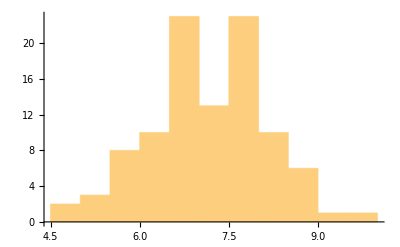

```mathematica
Histogram[meansBS, 10]
```

Look at different levels of repetition :

```mathematica
repetitionsList = {3, 30, 100, 1000, 10000};
```

```mathematica
i=10; 
a = Table[ Table[Table[RandomChoice[onlyYellowSpots[[All,i]]],sampleSize],repetitionsList[[num]] ], {num,1,Length@repetitionsList}];
```

```mathematica
meansBS = N/@Table[Table[Mean[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}];
stdevsBS = N/@StandardDeviation/@meansBS ;
errorBS =ErrorBar/@stdevsBS;
Length@meansBS
Length@stdevsBS
```

5

5

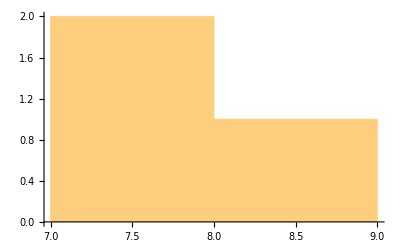
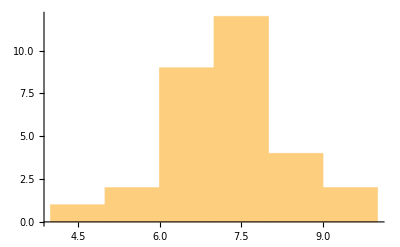
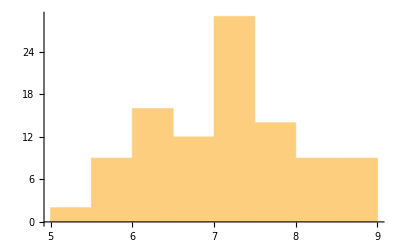
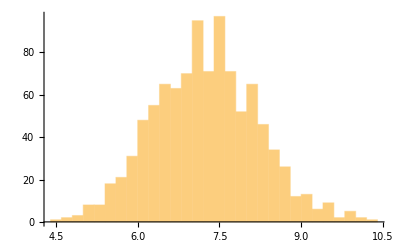
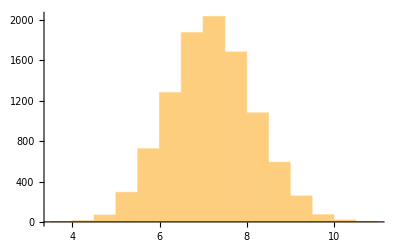

```mathematica
Histogram/@meansBS
```

#### Resampling and graphing a time series

Do bootstrapping on each point in a time series to determine error intervals

```mathematica
a = Table[Table[Table[RandomChoice[onlyYellowSpots[[All,i]]],sampleSize],repetitions ],{i,1,Length@onlyYellowSpots[[1]],1}];
```

```mathematica
meansBS = N/@Table[Table[Mean[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}];
mediansBS = N/@Table[Table[Median[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}];
stdevsBS = N/@StandardDeviation/@meansBS ;
stdevsBSMedians = N/@StandardDeviation/@mediansBS ;
errorBS =ErrorBar/@stdevsBS;
errorBSmedians =ErrorBar/@stdevsBSMedians;
Length@meansBS
Length@stdevsBS
```

65

65

```mathematica
c = Table[times,repetitions]//Transpose;
```

```mathematica
Length@c
Length/@c
```

65

{1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000}

```mathematica
repTimes = Table[times,repetitions]//Transpose;
medianTimeBS = Table[Transpose[{repTimes[[i]],mediansBS[[i]]}],{i,1,Length@mediansBS,1}]; 
meanTimeBS = Table[Transpose[{repTimes[[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];
```

```mathematica
b = Transpose[{myYelOnlySpotTime ,errorBS}];
```

```mathematica
repBS = ListPlot[
meanTimeBS,PlotLabel->{"All BS means at each time point" +repetitions ,"repetitions"}]
```

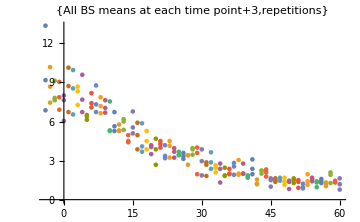
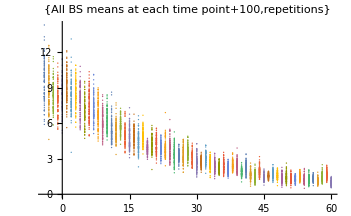
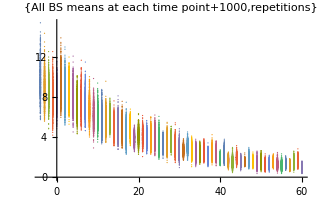
```mathematica
-Graphics--Graphics--Graphics--Graphics-
```

```mathematica
ErrorListPlot[b,PlotStyle->{Darker[Yellow]}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True]
```

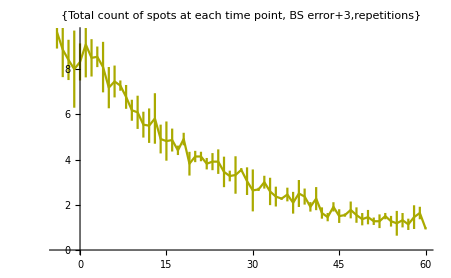
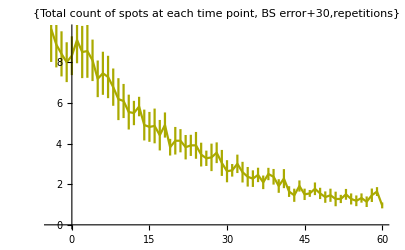
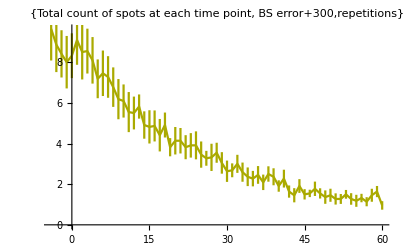
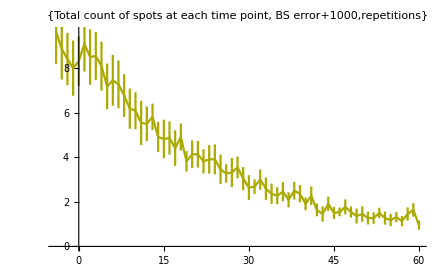
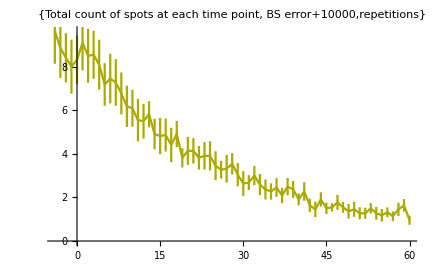

### BS for Purple Spots: (Don’t shift+entr)

```mathematica
purple//Dimensions
```

{22,65,2}

```mathematica
purple = purple[[All,All,2]];
```

```mathematica
a = Table[Table[Table[RandomChoice[purple[[All,i]]],sampleSize],repetitions ],{i,1,Length@purpleSpotCount,1}];
```

```mathematica
meansBS = N/@Table[Table[Mean[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}];
stdevsBS = N/@StandardDeviation/@meansBS 
errorBS =ErrorBar/@stdevsBS;
Length@meansBS
Length@stdevsBS
```

{4.12527,4.1539,3.53324,2.78547,2.97732,3.75319,3.66152,3.10635,3.18005,2.90694,2.48818,3.73596,3.48332,3.46991,3.18147,4.33107,3.36092,3.48487,3.09454,3.96222,2.4668,3.38366,3.17024,3.57048,3.26978,3.43109,2.72474,3.10206,2.49506,3.81188,3.33623,3.42165,2.79752,3.23162,3.04943,3.08647,3.72838,3.70314,3.34112,2.7966,2.95366,3.49063,3.22522,3.1883,2.96447,2.73833,2.51457,3.45841,2.74142,3.06279,3.61657,2.47502,3.1035,3.54071,3.17298,3.5129,2.99646,2.92408,2.6487,2.9008,3.8811,3.0326,3.1289,2.51594,3.4964}

65

65

```mathematica
meansBS[[1]]
Length/@meansBS
```

{25.0909,12.0909,9.04545,18.6818,13.1818,17.7727,13.8636,18.5,8.81818,15.8182,20.1364,16.6364,14.5909,19.7727,14.7727,12.6364,24.8182,15.,12.5909,13.6818,22.8636,16.7273,19.8182,12.0455,16.5,10.5455,13.2273,18.1818,17.1818,17.6364}

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
c = Table[times,repetitions]//Transpose;
```

```mathematica
Length@c
Length/@c
```

65

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
repTimes = Table[times,repetitions]//Transpose;
meanTimeBS = Table[Transpose[{repTimes[[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];
```

```mathematica
b = Transpose[{purpleTime ,errorBS}];
```

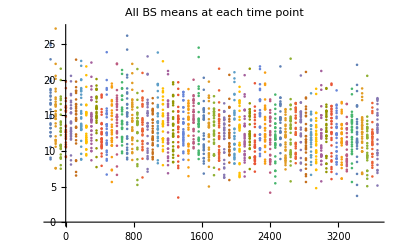

```mathematica
ListPlot[
meanTimeBS,PlotLabel->"All BS means at each time point"]
```

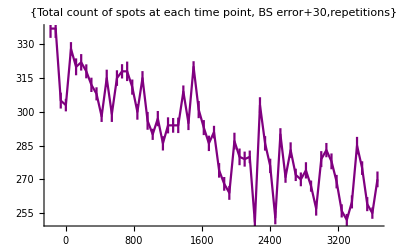

```mathematica
ErrorListPlot[b,PlotStyle->{Purple}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True]
```